## Helper Functions

```mathematica
P:=Table[KroneckerDelta[j,k]-{1,0,0}[[j]]{1,0,0}[[k]],{j,1,3},{k,1,3}]
TT[T_]:=Table[Sum[Sum[P[[a,j]] P[[b,k]] T[[j,k]] - 1/2 P[[a,b]](P[[j,k]] T[[k,j]]),{j,1,3}],{k,1,3}],{a,1,3},{b,1,3}]
STT[T_]:=S[TT[T]]
S[T_]:=1/2(T+Transpose[T])
gL2[r_,θ_]:={{r^2,0},{0,(r*Sin[θ])^2}}
gL[r_,θ_]:={{1,0,0},{0,r^2,0},{0,0,(r*Sin[θ])^2}}
gU[r_,θ_]:=Inverse[gL[r,θ]]
gU2[r_,θ_]:=Inverse[gL2[r,θ]]
lc2[r_,θ_]:={{0, √Det[gL[r,θ]] },{-√Det[gL[r,θ]],0}}
lc[r_,θ_]:= LeviCivitaTensor[3]*√Det[gL[r,θ]]
n:={1,0,0}
vars[r_,θ_,ϕ_]:={r,θ,ϕ}
Γ[r_,θ_,ϕ_,a_,b_,c_]:=Sum[1/2 gU[r,θ][[a,d]](D[gL[r,θ][[d,c]],vars[r,θ,ϕ][[b]]]+D[gL[r,θ][[b,d]],vars[r,θ,ϕ][[c]]]-D[gL[r,θ][[b,c]],vars[r,θ,ϕ][[d]]]),{d,1,3}] (* a is upper*)
covD[r_,θ_,ϕ_,τ_,a_,b_,c_]:=D[τ[[a,b]],vars[r,θ,ϕ][[c]]]-Sum[Γ[r,θ,ϕ,d,a,c] τ[[d,b]]+Γ[r,θ,ϕ,d,b,c] τ[[a,d]],{d,1,3}] (*a, b are tensor indices, c is differentiation variable*)
maxRealEigenvalue[T_]:=Max[Re@Chop@Eigenvalues[T]]
```

## Metric Perturbations

### Mass

```mathematica
hM[t_,r_,θ_,ϕ_,l_,m_,M_,Ω_,ω_]:=1/r(D[IMom[t,r,M,Ω,ω],{t,l}]*TE2STT[t,r, θ,ϕ,l,m])
TE2STT[t_,r_, θ_,ϕ_,l_,m_]:=(2((l-2)!)/((l+2)!))^(1/2)STT[r^2 Grad[Grad[SphericalHarmonicY[l,m,θ,ϕ],{r,θ,ϕ}, "Spherical"],{r,θ,ϕ}, "Spherical"]]
IMom[t_,r_,M_,Ω_,ω_]:=M ⅇ^(-ⅈ (Ω (t-r)+ω))
```

### Current

```mathematica
hC[t_,r_,θ_,ϕ_,l_,m_,M_,Ω_,ω_]:=1/r(D[SMom[t,r,M,Ω,ω,l],{t,l}]*TB2STT[t,r, θ,ϕ,l,m])
TB2STT[t_,r_, θ_,ϕ_,l_,m_]:= S[Table[Sum[Sum[
lc[r,θ][[i,β,α]] n[[β]] TE2STT[t,r,θ, ϕ, l, m][[α,j]],{α,1,3}],{β,1,3}],{i,1,3},{j,1,3}]]
SMom[t_,r_,M_,Ω_,ω_,l_]:=-M ⅇ^(-ⅈ (Ω (t-r)+ω))
```

## Electric and Magnetic

```mathematica
EField[h_,t_,r_,θ_,ϕ_,M_,Ω_,ω_]:=Refine[ComplexExpand[Re[-1/2 D[h[t,r,θ,ϕ,M,Ω,ω],{t,2}]]],{t,r,θ,ϕ,M,Ω,ω} ∈Reals]
BField[h_,t_,r_,θ_,ϕ_,M_,Ω_,ω_]:=Refine[ComplexExpand[Re[STT[Table[Sum[Sum[Sum[Sum[
lc[r,θ][[i,p,q]]gU[r,θ][[p,k]] gU[r,θ][[q,s]]  (D[covD[r,θ,ϕ,h[t,r,θ,ϕ,M,Ω,ω],s,j,k]-covD[r,θ,ϕ,h[t,r,θ,ϕ,M,Ω,ω],k,j,s],t])
,{p,1,3}],{q,1,3}],{k,1,3}],{s,1,3}],{i,1,3},{j,1,3}]]]],{t,r,θ,ϕ,M,Ω,ω} ∈Reals]
```

## Electric and Magnetic Declarations l = 2-5

```mathematica
hC22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hC[t,r,θ,ϕ,2,2,M,Ω,ω];
hM22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hM[t,r,θ,ϕ,2,2,M,Ω,ω] ;
hC33[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hC[t,r,θ,ϕ,3,3,M,Ω,ω];
hM33[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hM[t,r,θ,ϕ,3,3,M,Ω,ω] ;
hC44[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hC[t,r,θ,ϕ,4,4,M,Ω,ω];
hM44[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hM[t,r,θ,ϕ,4,4,M,Ω,ω] ;
hC55[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hC[t,r,θ,ϕ,5,5,M,Ω,ω];
hM55[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=hM[t,r,θ,ϕ,5,5,M,Ω,ω] ;
```

```mathematica
EMField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hM22,t,r,θ,ϕ,M,Ω,ω] ;
BMField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hM22,t,r,θ,ϕ,M,Ω,ω] ;
ECField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hC22,t,r,θ,ϕ,M,Ω,ω] ;
BCField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hC22,t,r,θ,ϕ,M,Ω,ω] ;
EMField33[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hM33,t,r,θ,ϕ,M,Ω,ω] ;
BMField33[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hM33,t,r,θ,ϕ,M,Ω,ω] ;
ECField33[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hC33,t,r,θ,ϕ,M,Ω,ω] ;
BCField33[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hC33,t,r,θ,ϕ,M,Ω,ω] ;EMField44[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hM44,t,r,θ,ϕ,M,Ω,ω] ;
BMField44[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hM44,t,r,θ,ϕ,M,Ω,ω] ;
ECField44[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hC44,t,r,θ,ϕ,M,Ω,ω] ;
BCField44[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hC44,t,r,θ,ϕ,M,Ω,ω] ;EMField55[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hM55,t,r,θ,ϕ,M,Ω,ω] ;
BMField55[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hM55,t,r,θ,ϕ,M,Ω,ω] ;
ECField55[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=EField[hC55,t,r,θ,ϕ,M,Ω,ω] ;
BCField55[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=BField[hC55,t,r,θ,ϕ,M,Ω,ω] ;
```

## Plots

```mathematica
NPoints=50;
```

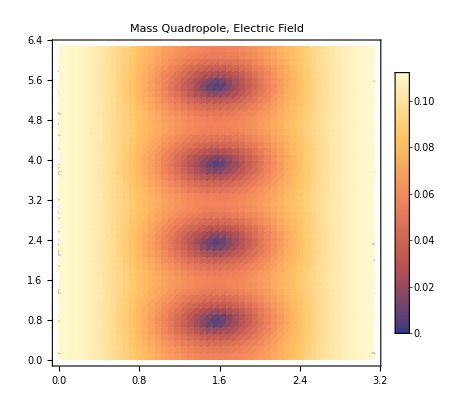

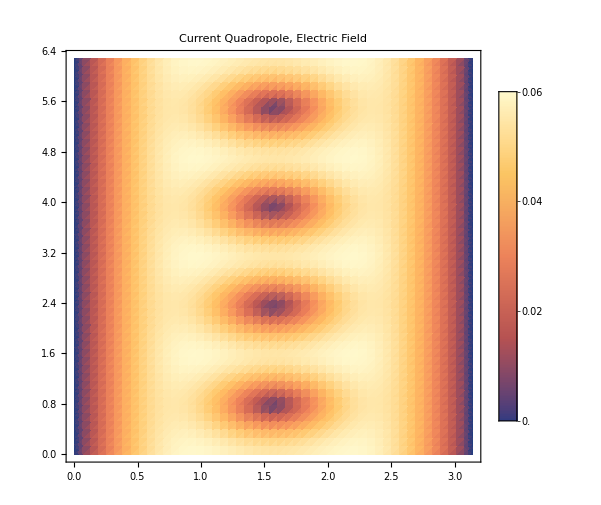

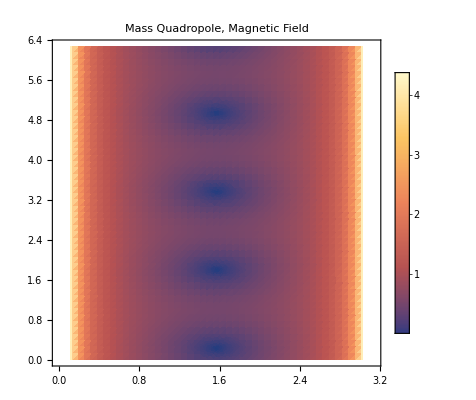

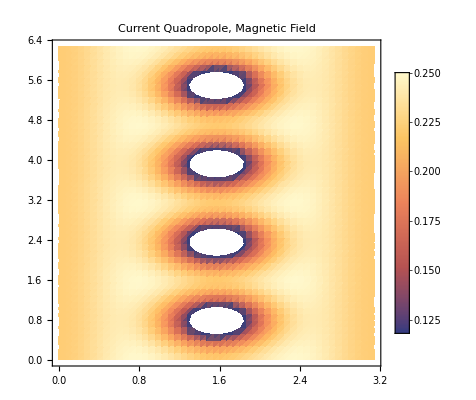

```mathematica
DensityPlot[maxRealEigenvalue[EMField22[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Quadropole, Electric Field",PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[ECField22[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Quadropole, Electric Field",PlotPoints->NPoints]
DensityPlot[maxRealEigenvalue[BMField22[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Quadropole, Magnetic Field",PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[BCField22[1.,1.,θ,ϕ,1.,1.,0.]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Quadropole, Magnetic Field",PlotPoints->NPoints]
```

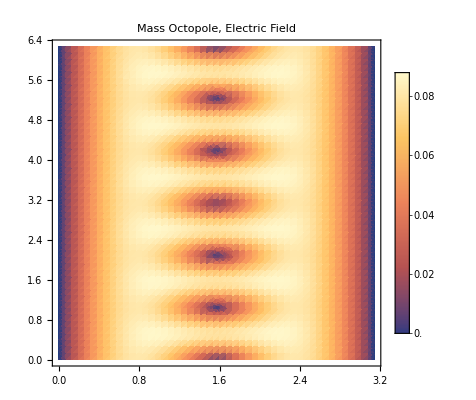

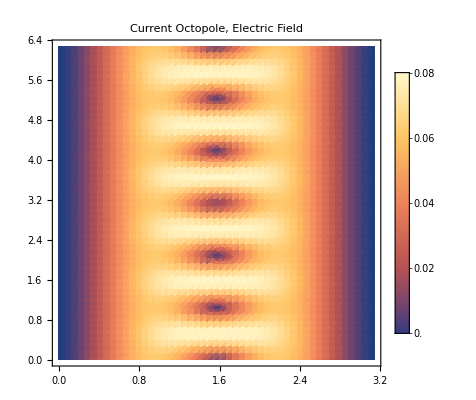

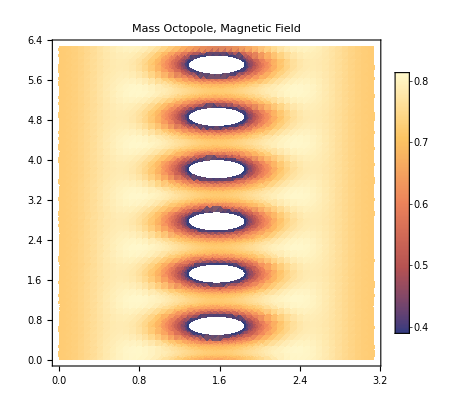

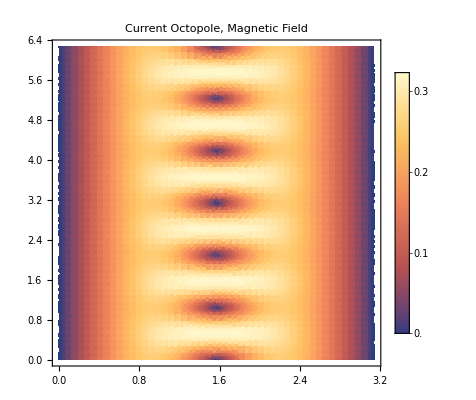

```mathematica
DensityPlot[maxRealEigenvalue[EMField33[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Octopole, Electric Field",PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[ECField33[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Octopole, Electric Field",PlotPoints->NPoints]
DensityPlot[maxRealEigenvalue[BMField33[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Octopole, Magnetic Field",PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[BCField33[1.,1.,θ,ϕ,1.,1.,0.]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Octopole, Magnetic Field",PlotPoints->NPoints]
```

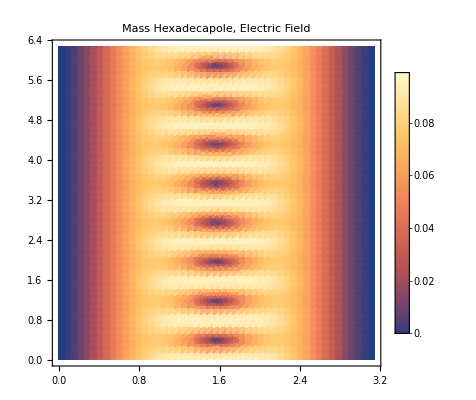

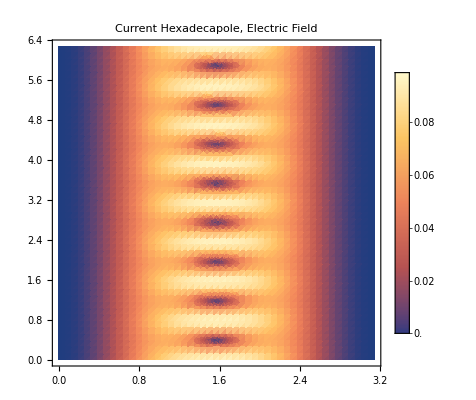

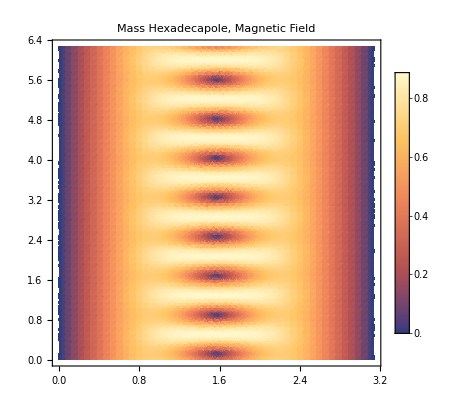

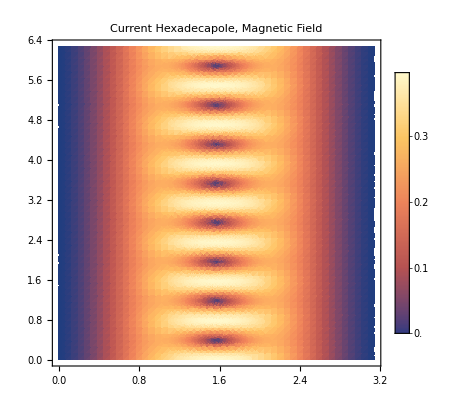

```mathematica
DensityPlot[maxRealEigenvalue[EMField44[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Hexadecapole, Electric Field", PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[ECField44[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Hexadecapole, Electric Field", PlotPoints->NPoints]
DensityPlot[maxRealEigenvalue[BMField44[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Hexadecapole, Magnetic Field", PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[BCField44[1.,1.,θ,ϕ,1.,1.,0.]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Hexadecapole, Magnetic Field", PlotPoints->NPoints]
```

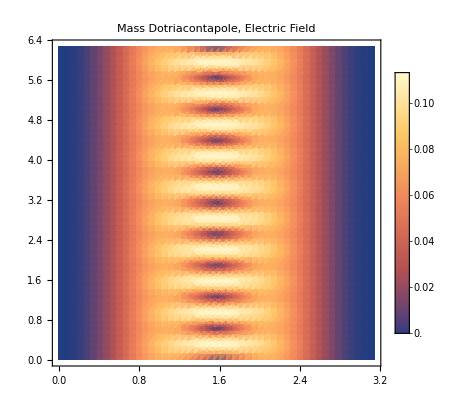

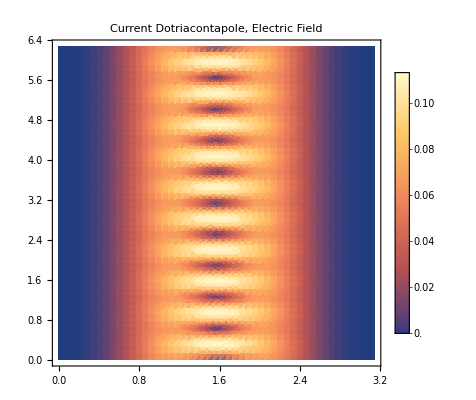

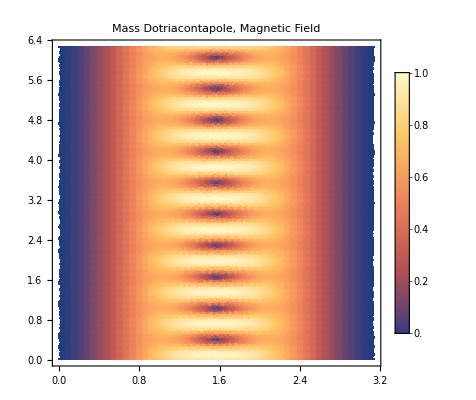

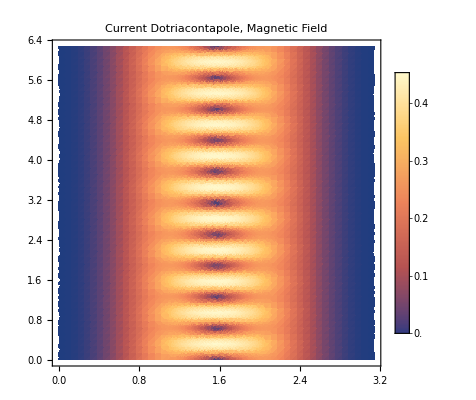

```mathematica
DensityPlot[maxRealEigenvalue[EMField55[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Dotriacontapole, Electric Field", PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[ECField55[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Dotriacontapole, Electric Field", PlotPoints->NPoints]
DensityPlot[maxRealEigenvalue[BMField55[1.,1.,θ,ϕ,1.,1.,0.] ], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic, PlotLabel->"Mass Dotriacontapole, Magnetic Field", PlotPoints->NPoints]
DensityPlot[ maxRealEigenvalue[BCField55[1.,1.,θ,ϕ,1.,1.,0.]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Current Dotriacontapole, Magnetic Field", PlotPoints->NPoints]
```

```mathematica
QuadropoleSum[ω_,C_]:=DensityPlot[Max[Eigenvalues[EMField22[1.,1.,θ,ϕ,1.,1.,0.]+C ECField22[1.,1.,θ,ϕ,1.,1.,ω] ]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Mass Plus Current Quadropole, Electric part. ω_current= Pi/"<>ToString[Pi/ω]<>" C_current= "<> ToString[C], PlotPoints->NPoints]
OctopoleSum[ω_,C_]:=DensityPlot[Max[Eigenvalues[EMField33[1.,1.,θ,ϕ,1.,1.,0.]+C ECField33[1.,1.,θ,ϕ,1.,1.,ω] ]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Mass Plus Current Octopole, Electric part. ω_current=Pi/"<>ToString[Pi/ω]<>" C_current= "<> ToString[C], PlotPoints->NPoints]
HexadecapoleSum[ω_,C_]:=DensityPlot[Max[Eigenvalues[EMField44[1.,1.,θ,ϕ,1.,1.,0.]+C ECField44[1.,1.,θ,ϕ,1.,1.,ω] ]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Mass Plus Current Hexadecapole, Electric part. ω_current=Pi/"<>ToString[Pi/ω]<>" C_current= "<> ToString[C], PlotPoints->NPoints]
DotriacontapoleSum[ω_,C_]:=DensityPlot[Max[Eigenvalues[EMField55[1.,1.,θ,ϕ,1.,1.,0.]+C ECField55[1.,1.,θ,ϕ,1.,1.,ω] ]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Mass Plus Current Dotriacontapole, Electric part. ω_current=Pi/"<>ToString[Pi/ω]<>" C_current= "<> ToString[C], PlotPoints->NPoints]
```

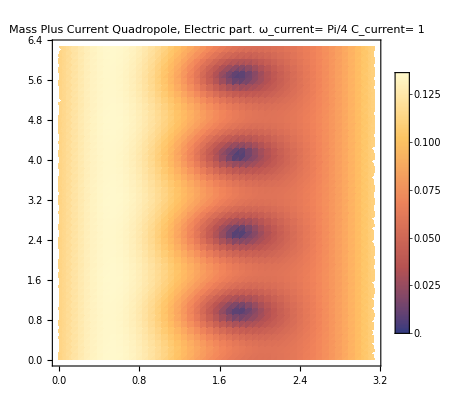

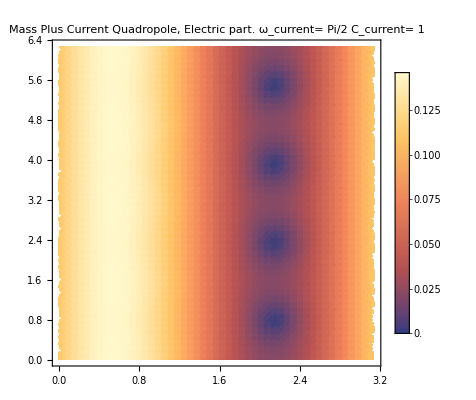

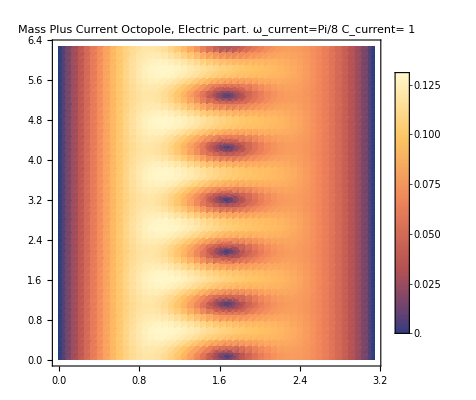

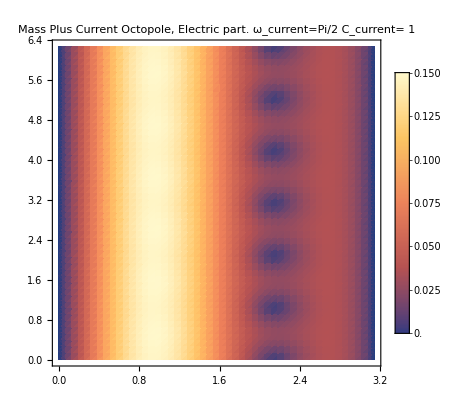

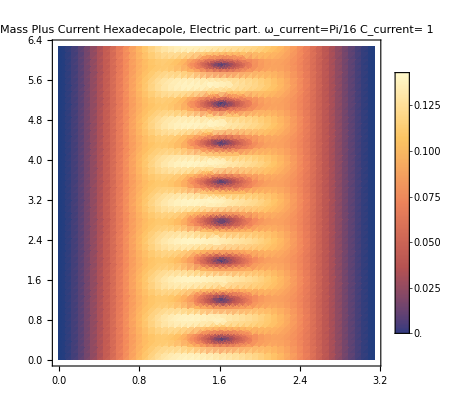

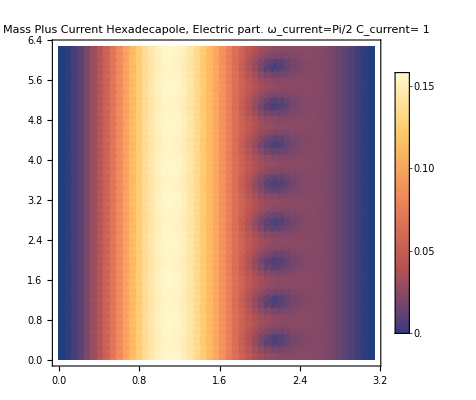

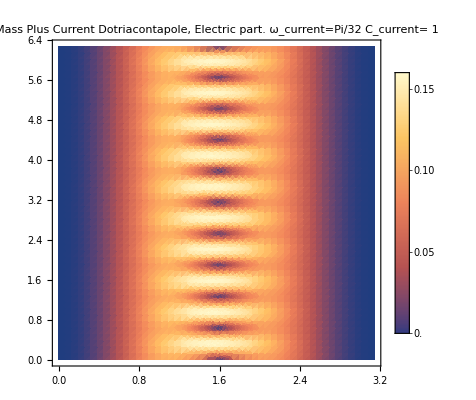

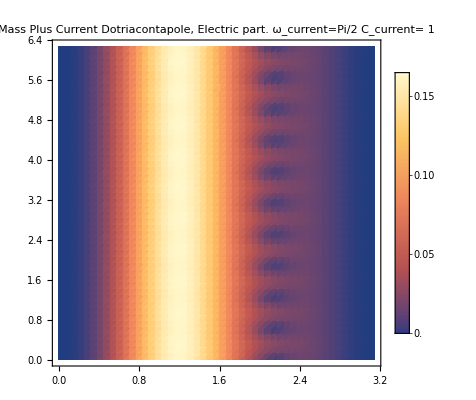

```mathematica
QuadropoleSum[Pi/4,1]
QuadropoleSum[Pi/2,1]
OctopoleSum[Pi/8,1]
OctopoleSum[Pi/2,1]
HexadecapoleSum[Pi/16,1]
HexadecapoleSum[Pi/2,1]
DotriacontapoleSum[Pi/32,1]
DotriacontapoleSum[Pi/2,1]
```

```mathematica
MultipoleLC[C2_,ω2_,C3_,ω3_,C4_,ω4_,C5_,ω5_,C6_,ω6_,C7_,ω7_,C8_,ω8_]:=C2(EMField22[1.,1.,θ,ϕ,1.,1.,0.]+ECField22[1.,1.,θ,ϕ,1.,1.,ω2])+C3(EMField33[1.,1.,θ,ϕ,1.,1.,0.]+ECField33[1.,1.,θ,ϕ,1.,1.,ω3])+C4(EMField44[1.,1.,θ,ϕ,1.,1.,0.]+ECField44[1.,1.,θ,ϕ,1.,1.,ω4])+C5(EMField55[1.,1.,θ,ϕ,1.,1.,0.]+ECField55[1.,1.,θ,ϕ,1.,1.,ω5]) + C6(EMField44[1.,1.,θ,ϕ,1.,1.,0.]+ECField44[1.,1.,θ,ϕ,1.,1.,ω6])+C7(EMField55[1.,1.,θ,ϕ,1.,1.,0.]+ECField55[1.,1.,θ,ϕ,1.,1.,ω7]) + C8(EMField44[1.,1.,θ,ϕ,1.,1.,0.]+ECField44[1.,1.,θ,ϕ,1.,1.,ω8])
MultipoleLCPlot[C2_,ω2_,C3_,ω3_,C4_,ω4_,C5_,ω5_,C6_,ω6_,C7_,ω7_,C8_,ω8_]:=DensityPlot[Max[Eigenvalues[MultipoleLC[C2,ω2,C3,ω3,C4,ω4,C5,ω5,C6,ω6,C7,ω7,C8,ω8] ]], {θ, 0, Pi}, {ϕ, 0, 2*Pi},PlotLegends->Automatic,PlotLabel->"Multipole linear combination"]
MultipoleSum[C_,ω_,n_,θ_,ϕ_]:=Sum[C[[i]](EMField[1.,1.,θ,ϕ,i,i,1.,1.,0.]+ECField[1.,1.,θ,ϕ,i,i,1.,1.,ω[[i]]]),{i,2,n+1}]
```

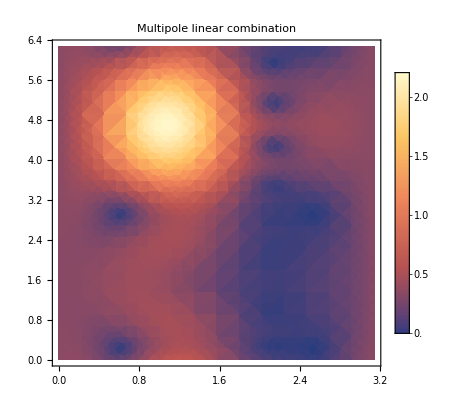

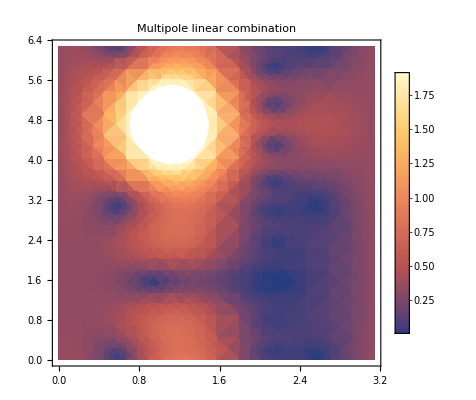

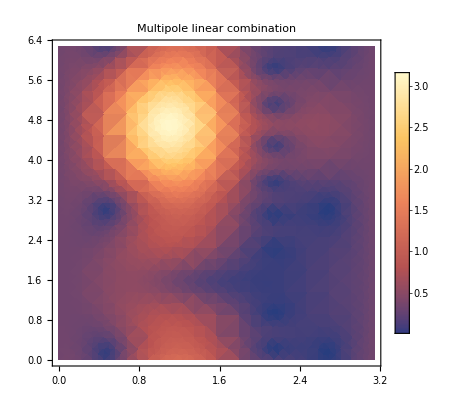

```mathematica
MultipoleLCPlot[1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,0,Pi/2,0,Pi/2]
MultipoleLCPlot[1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,0,Pi/2]
MultipoleLCPlot[1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2,1,Pi/2]
```

## Super Poynting

```mathematica
EMField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=Simplify[EField[hM22,t,r,θ,ϕ,M,Ω,ω] ];
BMField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=Simplify[BField[hM22,t,r,θ,ϕ,M,Ω,ω] ];
ECField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=Simplify[EField[hC22,t,r,θ,ϕ,M,Ω,ω] ];
BCField22[t_,r_,θ_,ϕ_,M_,Ω_,ω_]=Simplify[BField[hC22,t,r,θ,ϕ,M,Ω,ω] ];
```

```mathematica
ESum2[C_,t_,r_,θ_,ϕ_,M_,Ω1_,Ω2_,ω_]:=EMField22[t,r,θ,ϕ,M,Ω1,0]+C ECField22[t,r,θ,ϕ,M,Ω2,ω]
BSum2[C_,t_,r_,θ_,ϕ_,M_,Ω1_,Ω2_,ω_]:=BMField22[t,r,θ,ϕ,M,Ω1,0]+C BCField22[t,r,θ,ϕ,M,Ω2,ω]
ESum[C_,t_,r_,θ_,ϕ_,M_,Ω1_,Ω2_,ω_]:=EMField22[t,r,θ,ϕ,M,Ω1,0]
BSum[C_,t_,r_,θ_,ϕ_,M_,Ω1_,Ω2_,ω_]:=BMField22[t,r,θ,ϕ,M,Ω1,0]
SuperPoynting[C_,t_,r_,θ_,φ_,Ω1_,Ω2_]:=Table[Sum[Sum[Sum[Sum[
lc[r,θ][[i,j,k]]*gU[r,θ][[l,m]]*ESum[C,t,r,θ,φ,1,Ω1,Ω2,Pi/2][[j,m]]*BSum[C,t,r,θ,φ,1,Ω1,Ω2,Pi/2][[k,l]]
,{m,1,3}],{l,1,3}],{k,1,3}],{j,1,3}],{i,1,3}];
```

```mathematica
Simplify[SuperPoynting[1,t,r,θ,ϕ,Ω1,Ω2][[1]] /r^2 Sin[θ]]
```

1/(4096 π r^7)5 Ω1^7 Abs[Sin[θ]] √(r^4 Sin[θ]^2) ((3+Cos[2 θ]) Cos[2 ϕ+r Ω1-t Ω1] Csc[θ] (9-Cos[4 θ]+8 Abs[Sin[θ]]^2 Csc[θ]^2) (r Ω1 Cos[2 ϕ+r Ω1-t Ω1]-2 Sin[2 ϕ+r Ω1-t Ω1])+(3+Cos[2 θ]) Cos[2 ϕ+r Ω1-t Ω1] Csc[θ]^3 (9-Cos[4 θ]+8 Abs[Sin[θ]]^2 Csc[θ]^2) (r Ω1 Cos[2 ϕ+r Ω1-t Ω1]-2 Sin[2 ϕ+r Ω1-t Ω1])+64 Cos[θ] Cot[θ] (1+Abs[Sin[θ]]^2 Csc[θ]^4) Sin[2 ϕ+r Ω1-t Ω1] (2 Cos[2 ϕ+r Ω1-t Ω1]+r Ω1 Sin[2 ϕ+r Ω1-t Ω1])+64 Cos[θ]^2 (1+Abs[Sin[θ]]^2 Csc[θ]^4) Sin[θ] Sin[2 ϕ+r Ω1-t Ω1] (2 Cos[2 ϕ+r Ω1-t Ω1]+r Ω1 Sin[2 ϕ+r Ω1-t Ω1]))

```mathematica
SIntegral[θ_, ϕ_,a_]:=NIntegrate[SuperPoynting[1,1.,1.,θ0,φ0,1.,1.][[1]]  Sin[θ0],{θ0,θ-a/2,θ+a/2},{φ0,ϕ-a,ϕ+a}]
```

```mathematica
θMin=0;
θMax=Pi;
ϕMin=0;
ϕMax=2 Pi;
NPoints = 5;
a=(θMax-θMin)/NPoints;
DensityPlot[SIntegral[θ, ϕ,a],{θ,0,Pi},{ϕ,0,2 Pi},PlotPoints->NPoints]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in θ0 near {θ0,φ0} = {1.25624×10^-6,0.434009}. NIntegrate obtained 6.49064 and 15.5016 for the integral and error estimates.

```mathematica
-Graphics-rw2`
```

## Spin Weighted Spherical Harmonics

```mathematica
Y[s_,l_,m_,θ_,ϕ_]:=(-1)^m Simplify[√(((l+m)!(l-m)!(2l+1))/((l+s)!(l-s)!4π))(Sin[θ/2])^(2l)∑_(r=0)^(l-s) (Binomial[l-s,r]Binomial[l+s,r+s-m](-1)^(l-r-s)ⅇ^(ⅈ m ϕ)(Cot[θ/2])^(2r+s-m)),Assumptions->{ϕ∈Reals,θ∈Reals}]
```

```mathematica
TE2a[l_,m_,θ_,ϕ_]:= 1/2^1.5(Y[-2,l,m,θ,ϕ] + Y[2,l,m,θ,ϕ])
TE2b[l_,m_,θ_,ϕ_]:=ⅈ/2^1.5(Y[-2,l,m,θ,ϕ] - Y[2,l,m,θ,ϕ])
TE2Test[l_,m_,θ_,ϕ_]:={{TE2a[l,m,θ,ϕ],TE2b[l,m,θ,ϕ]}, {TE2b[l,m,θ,ϕ], -TE2a[l,m,θ,ϕ]}}
SMom[t_,r_,M_,Ω_,ω_,l_]:=-M ⅇ^(-ⅈ (Ω (t-r)+ω))
a[θ_,ϕ_]=TE2STT[1,r,θ,ϕ,2,2];
b[θ_,ϕ_]=SMom[0, 1, 1, 1, Pi/2, 0]TE2Test[2,2,θ,ϕ];
```

```mathematica
SMom[0, 1, 1., 1, Pi/2, 0]
```

-0.841471+0.540302 ⅈ

```mathematica
TestEigenA[θ_,ϕ_]:=Max[Eigenvalues[Refine[ComplexExpand[Re[a[θ,ϕ]]],{θ,ϕ}∈Reals]]]
TestEigenB[θ_,ϕ_]:=Max[Eigenvalues[Refine[ComplexExpand[Re[b[θ,ϕ]]],{θ,ϕ}∈Reals]]]
```

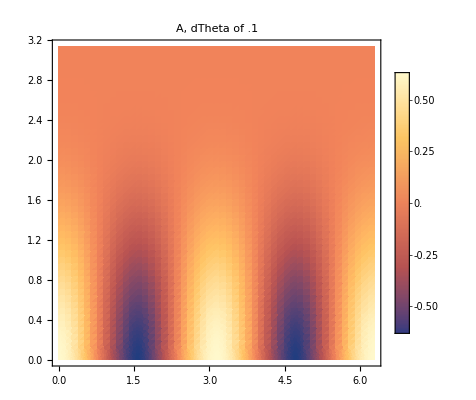

```mathematica
DensityPlot[Refine[ComplexExpand[Re[Y[-2,2,2,θ,ϕ]]],{θ,ϕ} ∈Reals], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"A, dTheta of .1",PlotPoints->50]
```

-Graphics-

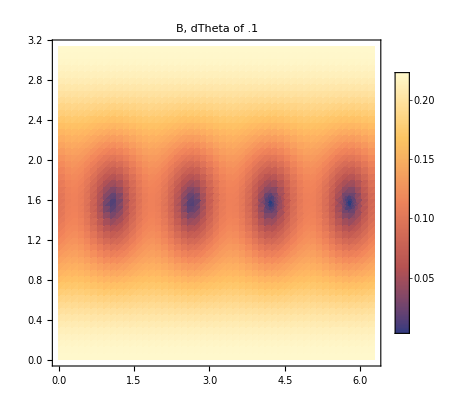

```mathematica
DensityPlot[TestEigenA[θ,ϕ], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"A, dTheta of .1",PlotPoints->50]
DensityPlot[TestEigenB[θ,ϕ], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"B, dTheta of .1",PlotPoints->50]
```

## Test

```mathematica
PU[r_,θ_] := Table[Sum[gL[r,θ][[a,c]] P[[i,c]],{c,1,3}],{a,1,3},{i,1,3}]
xHat[θ_, ϕ_]:={Sin[θ] Cos[ϕ],Cos[θ] Cos[ϕ], -Sin[ϕ]}
yHat[θ_,ϕ_]:={Sin[θ] Sin[ϕ],Cos[θ] Sin[ϕ], Cos[ϕ]}
E0[λ_,R_,θ_,ϕ_, dθ_]:=Simplify[STT[λ{{0, 0, 0}, {0, Cos[2 ϕ] Cos[θ]^2, -Sin[2 ϕ]Cos[θ]}, {0,  -Sin[2 ϕ]Cos[θ],Cos[2 ϕ] }}Exp[-θ^2/(2 dθ)]]]
```

```mathematica
Refine[ComplexExpand[Re[E0[λ,1.,θ,ϕ,dθ]]],{λ,θ,ϕ,dθ}∈Reals] // MatrixForm
```

(0 | 0 | 0
0 | -(λ Cos[2 ϕ] Sin[θ]^2)/(2 √(ⅇ^(θ^2/dθ))) | -(λ Cos[θ] Sin[2 ϕ])/(√(ⅇ^(θ^2/dθ)))
0 | -(λ Cos[θ] Sin[2 ϕ])/(√(ⅇ^(θ^2/dθ))) | (λ Cos[2 ϕ] Sin[θ]^2)/(2 √(ⅇ^(θ^2/dθ))))

```mathematica
EEigen[λ_,dθ_,θ_,ϕ_]=Max[Eigenvalues[Refine[ComplexExpand[Re[E0[λ,1.,θ,ϕ,dθ]]],{λ,θ,ϕ,dθ}∈Reals]]]
```

Max[0,-(λ √(38+24 Cos[2 θ]+2 Cos[4 θ]-20 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-26 Cos[4 ϕ]-20 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]))/(8 √2 √(ⅇ^(θ^2/dθ))),(λ √(38+24 Cos[2 θ]+2 Cos[4 θ]-20 Cos[2 θ-4 ϕ]+Cos[4 θ-4 ϕ]-26 Cos[4 ϕ]-20 Cos[2 θ+4 ϕ]+Cos[4 θ+4 ϕ]))/(8 √2 √(ⅇ^(θ^2/dθ)))]

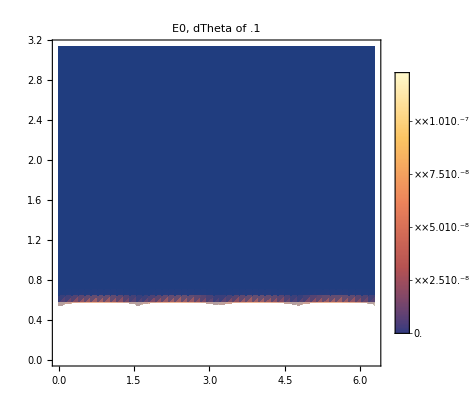

-Graphics3D-

```mathematica
λ0=1;
dθ0=.01;
DensityPlot[EEigen[λ0,dθ0,θ,ϕ], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"E0, dTheta of .1",PlotPoints->50]
SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},ColorFunction->Function[{x,y,z,θ,ϕ},ColorData["TemperatureMap"][EEigen[λ0,dθ0,θ,ϕ]]],ColorFunctionScaling->False,Mesh->None,Lighting->"Neutral",PlotPoints->50]
```

```mathematica
M:={0,1,ⅈ}
MBar:={0,1,-ⅈ}
E0[λ_, dθ_,θ_,ϕ_]:=Simplify[STT[λ{{0, 0, 0}, {0, Cos[2 ϕ] Cos[θ]^2, -Sin[2 ϕ]Cos[θ]}, {0,  -Sin[2 ϕ]Cos[θ],Cos[2 ϕ] }}Exp[-θ^2/(2 dθ)]]]
sYlm[s_,l_,m_,θ_,ϕ_]:=(-1)^m √(((l+m)!(l-m)!(2l+1))/((l+s)!(l-s)!4π))(Sin[θ/2])^(2l)∑_(r=0)^(l-s) (Binomial[l-s,r]Binomial[l+s,r+s-m](-1)^(l-r-s)ⅇ^(ⅈ m ϕ)(Cot[θ/2])^(2r+s-m))
AIntegrand[l_,m_, λ_, dθ_,θ_,ϕ_]:=Simplify[Sum[Sum[
E0[λ, dθ,θ,ϕ] [[i,j]]Conjugate[ M[[i]] M[[j]] sYlm[-2,l,m,θ,ϕ] + MBar[[i]] MBar[[j]] sYlm[2,l,m,θ,ϕ]] Sin[θ],{i,1,3}],{j,1,3}]  ]
A[l_,m_, λ_, dθ_]:=NIntegrate[AIntegrand[l,m, λ, dθ,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi}]
BIntegrand[l_,m_, λ_, dθ_,θ_,ϕ_]:=Simplify[Sum[Sum[
E0[λ, dθ,θ,ϕ] [[i,j]]Conjugate[ -ⅈ(M[[i]] M[[j]] sYlm[-2,l,m,θ,ϕ] - MBar[[i]] MBar[[j]] sYlm[2,l,m,θ,ϕ])] Sin[θ],{i,1,3}],{j,1,3}]  ]
B[l_,m_, λ_, dθ_]:=NIntegrate[BIntegrand[l,m, λ, dθ,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi}]
```

```mathematica
lMax=2;
threshold=10^-8;
λ = 1;
dθ = .1;
Amodes = {};
Bmodes = {};
Do[Module[{a, b},
a=A[l,m,λ,dθ];
b=B[l,m,λ,dθ];
If[Abs[a]>threshold,AppendTo[Amodes,{l,m,a}]];
If[Abs[b]>threshold,AppendTo[Bmodes,{l,m,b}]];],{l,2,lMax},{m,2,2}]
```

Part::partw: Part 2 of STT[{{0,0,0},{0,ⅇ^(-5. θ^2) Cos[θ]^2 Cos[2 ϕ],-2 ⅇ^(-5. θ^2) Cos[θ] Cos[ϕ] Sin[ϕ]},{0,-2 ⅇ^(-5. θ^2) Cos[θ] Cos[ϕ] Sin[ϕ],ⅇ^(-5. θ^2) Cos[2 ϕ]}}] does not exist.

Part::partw: Part 3 of STT[{{0,0,0},{0,ⅇ^(-5. θ^2) Cos[θ]^2 Cos[2 ϕ],-2 ⅇ^(-5. θ^2) Cos[θ] Cos[ϕ] Sin[ϕ]},{0,-2 ⅇ^(-5. θ^2) Cos[θ] Cos[ϕ] Sin[ϕ],ⅇ^(-5. θ^2) Cos[2 ϕ]}}] does not exist.

Part::partw: Part 2 of STT[{{0,0,0},{0,ⅇ^(-5. θ^2) Cos[θ]^2 Cos[2 ϕ],-2 ⅇ^(-5. θ^2) Cos[θ] Cos[ϕ] Sin[ϕ]},{0,-2 ⅇ^(-5. θ^2) Cos[θ] Cos[ϕ] Sin[ϕ],ⅇ^(-5. θ^2) Cos[2 ϕ]}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1/8 ⅇ^(-2 ⅈ Conjugate[ϕ]) √(5/π) (-4 ⅈ Conjugate[Cos[θ]] (STT[{{«3»},{«3»},{«3»}}]⟦2,3⟧+STT[{{«3»},{«3»},{«3»}}]⟦3,2⟧)+(3+Cos[2 Conjugate[θ]]) (-STT[{«3»}]⟦3,3⟧+STT[{{«3»},{«3»},{«3»}}]⟦2,2⟧)) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Amodes
```

{}

```mathematica
Amodes={{2,2,0.2903973386805203},{3,2,0.2647860722137299},{4,2,0.2033605554724347},{5,2,0.12379732106313937},{6,2,0.04304598622261916},{7,2,-0.02634305225678242+5.605786745327606*^-13 ⅈ},{8,2,-0.07809271004816035+6.613633252161577*^-18 ⅈ},{9,2,-0.1116385967245462+4.255493527005605*^-18 ⅈ},{10,2,-0.13000645859810248-7.888709217113155*^-15 ⅈ},{11,2,-0.13749108829651047+2.2911234312771417*^-13 ⅈ},{12,2,-0.1380597472233879+4.7704895589362195*^-18 ⅈ}};
Bmodes={{2,2,-3.7358950568527893*^-13+0.2935066033927123 ⅈ},{3,2,3.525518120712015*^-12+0.2803482326691428 ⅈ},{4,2,-5.9631119486702744*^-18+0.2459262376518366 ⅈ},{5,2,-3.354868466365346*^-14+0.20807822680388235 ⅈ},{6,2,6.431031922271568*^-14+0.17807240773275948 ⅈ},{7,2,2.2768245622195593*^-18+0.15960236405029898 ⅈ},{8,2,2.72405795836983*^-18+0.15082456535704694 ⅈ},{9,2,6.505213034913027*^-19+0.14760658092640253 ⅈ},{10,2,2.7896711633432214*^-14+0.14612542804996806 ⅈ},{11,2,-1.5212817840504537*^-12+0.14403737820598086 ⅈ},{12,2,-5.931534560396634*^-15+0.14046898417948492 ⅈ}};
```

```mathematica
Amodes[[All,3]]
Bmodes[[All,3]]
```

{0.290397,0.264786,0.203361,0.123797,0.043046,-0.0263431+5.60579×10^-13 ⅈ,-0.0780927+6.61363×10^-18 ⅈ,-0.111639+4.25549×10^-18 ⅈ,-0.130006-7.88871×10^-15 ⅈ,-0.137491+2.29112×10^-13 ⅈ,-0.13806+4.77049×10^-18 ⅈ}

{-3.7359×10^-13+0.293507 ⅈ,3.52552×10^-12+0.280348 ⅈ,-5.96311×10^-18+0.245926 ⅈ,-3.35487×10^-14+0.208078 ⅈ,6.43103×10^-14+0.178072 ⅈ,2.27682×10^-18+0.159602 ⅈ,2.72406×10^-18+0.150825 ⅈ,6.50521×10^-19+0.147607 ⅈ,2.78967×10^-14+0.146125 ⅈ,-1.52128×10^-12+0.144037 ⅈ,-5.93153×10^-15+0.140469 ⅈ}

```mathematica
AMat[l_,m_,θ_,ϕ_]:=Table[M[[i]] M[[j]] sYlm[-2,l,m,θ,ϕ] + MBar[[i]] MBar[[j]] sYlm[2,l,m,θ,ϕ],{i,1,3},{j,1,3}]
BMat[l_,m_,θ_,ϕ_]:=Table[-ⅈ(M[[i]] M[[j]] sYlm[-2,l,m,θ,ϕ] - MBar[[i]] MBar[[j]] sYlm[2,l,m,θ,ϕ]),{i,1,3},{j,1,3}]
```

```mathematica
summation[θ_,φ_]:=Sum[(Amodes[[n,3]] AMat[Amodes[[n,1]],Amodes[[n,2]],θ,φ]+Bmodes[[n,3]] BMat[Bmodes[[n,1]],Bmodes[[n,2]],θ,φ]),{n,1,Length[Amodes]}]
```

```mathematica
sumEigen[θ_,ϕ_]=Max[Eigenvalues[Refine[ComplexExpand[Re[summation[θ,ϕ]]],{λ,θ,ϕ,dθ}∈Reals]]]
```

Eigenvalues[0]

```mathematica
sumEigen[θ,ϕ]
```

General::munfl: 2.50962×10^-190 8.60483×10^-125 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

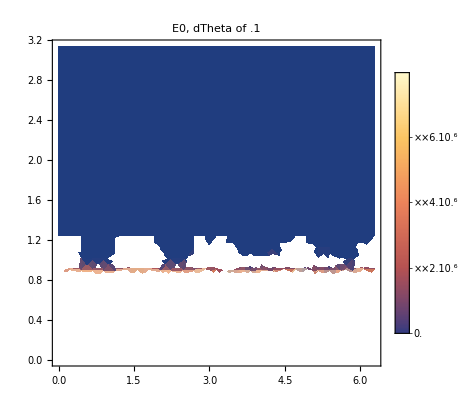

```mathematica
DensityPlot[sumEigen[θ,ϕ], {ϕ, 0, 2*Pi},{θ, 0, Pi},PlotLegends->Automatic, PlotLabel->"E0, dTheta of .1",PlotPoints->15]
```